## √2 Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
r2=RealDigits[Sqrt[2],10,10000][[1,2;;]];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[r2]
```

{0.194327,0.948796}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[r2];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→1,7→484,3→2156,6→684,8→358,14→97,5→982,4→1473,2→2367,10→227,18→44,12→132,15→77,17→42,23→24,9→337,11→187,25→12,28→4,16→56,13→108,20→30,31→4,21→18,19→33,29→6,22→16,32→3,35→2,24→15,26→4,30→3,27→6,36→1,34→2,37→1,41→1,33→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

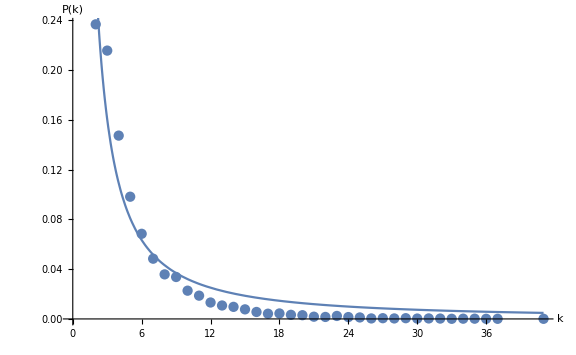
{{C→0.696971,γ→1.338},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[r2];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→1,5→923,2→3872,3→2268,6→609,4→1331,8→236,7→420,10→90,11→66,12→23,9→145,14→5,13→8,15→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

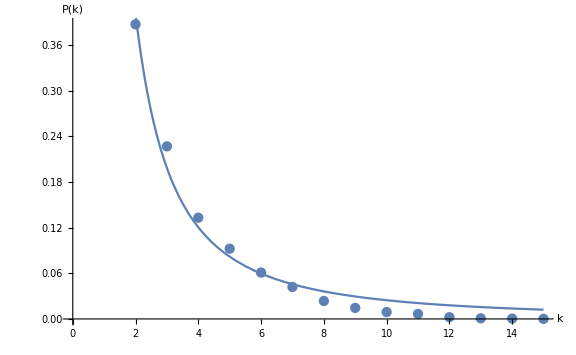
{{C→1.33435,γ→1.73472},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```